```mathematica
y[n_]:=1/n
phi[x_,n_]:=1/Pi*y[n]/(x^2+y[n]^2)
```

```mathematica
p =Plot[{phi[x,1],phi[x,2],phi[x,3],phi[x,4],phi[x,5],phi[x,6],phi[x,7]},{x,-4,4},PlotStyle->{RGBColor[0.403922, 0, 0.807843],RGBColor[0.203922, 0.341176, 0.619608],RGBColor[0, 0.501961, 0.752941],RGBColor[0.47451, 0.705882, 0.0470588],RGBColor[0.968627, 0.85098, 0.0352941],
RGBColor[1, 0.501961, 0.25098],RGBColor[0.662745, 0.0862745, 0.0862745]},
AspectRatio->1,
PlotRange-> {{-4.2, 4.3}, {0, 2.5}},
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},LabelStyle->(FontFamily->"STIX Two Text"),
PlotLegends->Placed[{Subscript[φ,1][x],Subscript[φ,2][x],Subscript[φ,3][x],Subscript[φ,4][x],Subscript[φ,5][x],Subscript[φ,6][x],Subscript[φ,7][x]},StatusArea]]
```

Placed::labpos: StatusArea is not a valid position for the placement of labels.

-Graphics-

```mathematica
Export["D:\\wolfram\\approx_2.pdf",p]
```

Placed::labpos: StatusArea is not a valid position for the placement of labels.

D:\wolfram\approx_2.pdf

```mathematica
c = ComplexPlot3D[Beta[1/2,z],{z,-2-2 I,2+2 I},PlotLegends->Automatic,LabelStyle->(FontFamily->"STIX Two Text")]
-Graphics3D-
Export["D:\\wolfram\\beta.pdf",c]
"D:\\wolfram\\beta.pdf"
```

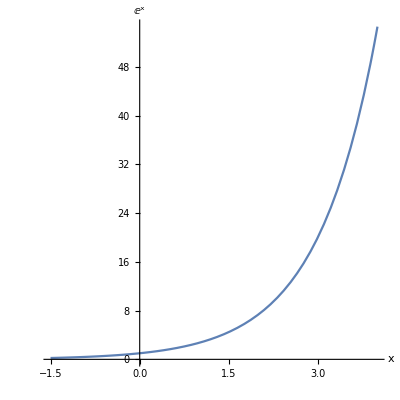

```mathematica
exp=Plot[Exp[x],{x,-1.5, 4}, AspectRatio->1, AxesLabel->{x,Exp[x]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}]
```

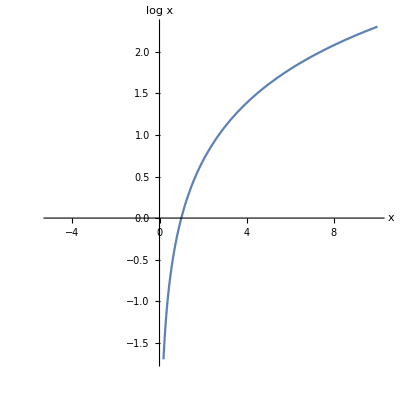

```mathematica
log=Plot[Log[x],{x, -5, 10}, AspectRatio->1,
 AxesLabel->{x,
Style["log",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}]
```

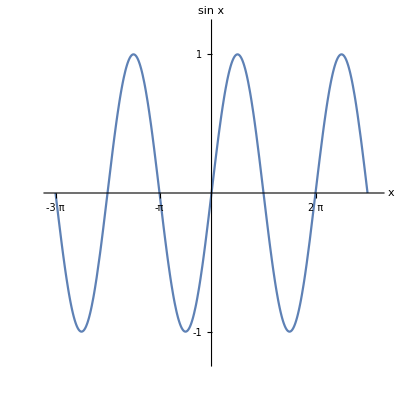

```mathematica
sin=Plot[Sin[x], {x, -3Pi, 3Pi}, AspectRatio->1, 
AxesLabel->{x,
Style["sin",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},
LabelStyle->{FontFamily->"STIX Two Text"},
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
Ticks->{{-3Pi,-2Pi,-Pi,Pi,2Pi,3Pi},{-1, 1}},
PlotRange->{{-3Pi-0.3, 3Pi+0.6},{-1.2, 1.2}}]
```

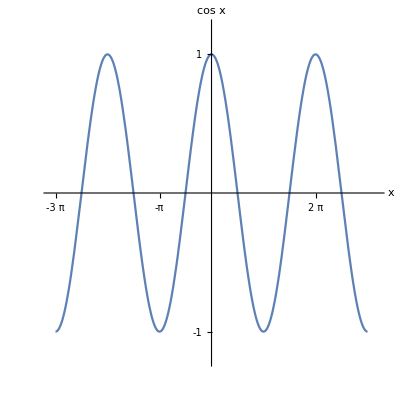

```mathematica
cos=Plot[Cos[x],{x,-3Pi, 3Pi}, AspectRatio->1, 
AxesLabel->{x,
Style["cos",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
Ticks->{{-3Pi,-2Pi,-Pi,Pi,2Pi,3Pi},{-1, 1}},
PlotRange->{{-3Pi-0.3, 3Pi+0.6},{-1.2, 1.2}}]
```

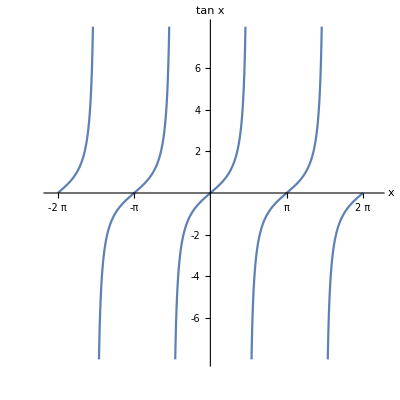

```mathematica
tan=Plot[Tan[x], {x, -2Pi, 2Pi}, 
 AspectRatio->1, 
AxesLabel->{x,
Style["tan",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
Ticks->{{-2Pi,-Pi,Pi,2Pi},{-6, -4,-2,2,4,6}},
PlotRange->{{-2Pi-0.3, 2Pi+0.6},{-8, 8}}]
```

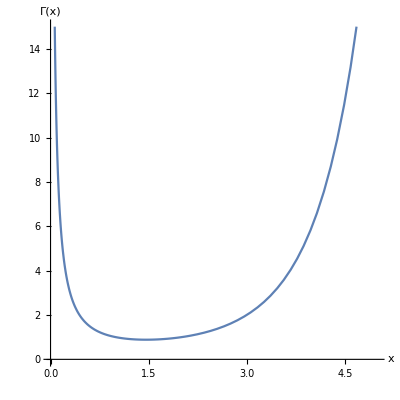

```mathematica
gamma=Plot[Gamma[x], {x, 0, 5}, 
PlotRange->{{0, 5},{0, 15}},
AspectRatio->1, 
AxesLabel->{x,Γ[x]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}]
```

```mathematica
Export["/home/slava/theory_university/imgs/task_4/gamma.pdf",gamma]
```

/home/slava/theory_university/imgs/task_4/gamma.pdf

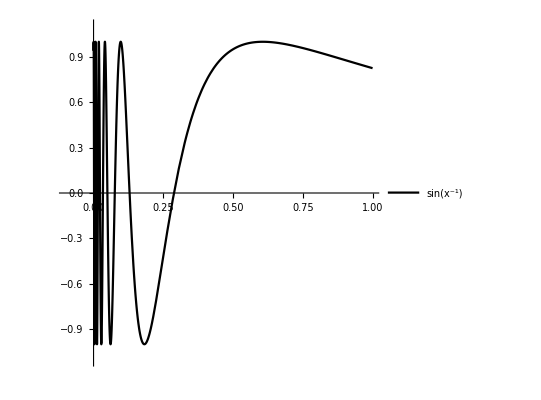

```mathematica
sin=Plot[{Sin[1/(x+0.03)]},
{x,0,1},
MaxRecursion->12,
AspectRatio->1,
Ticks->None,
PlotRange->{{-0.1,1},{-1.1,1.1}},
LabelStyle->(FontFamily->"STIX Two Text"),
PlotStyle->{Black},
PlotLegends->{Sin[Superscript[x,-1]]}]
```

```mathematica
text=Graphics[{Red, Style[Text[V,{-0.03,0.3}], FontFamily->"STIX Two Text",Italic],LabelStyle-> (FontFamily->"STIX Two Text")}]
```

-Graphics-

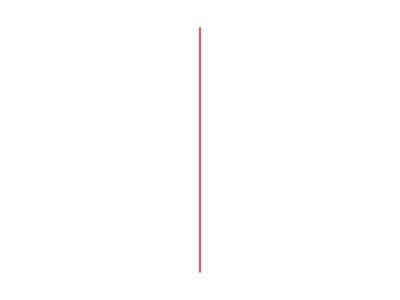

```mathematica
line=Graphics[{Thick,Red,Line[{{0,-1},{0,1}}]}]
```

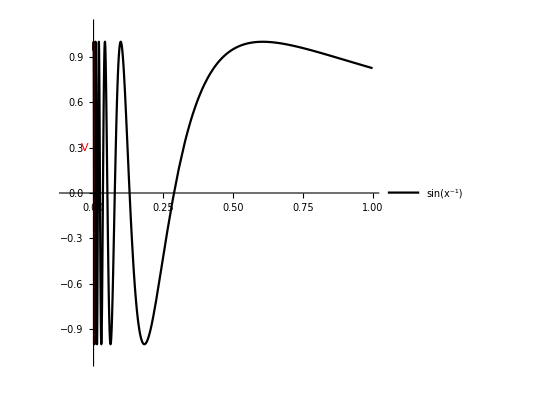

```mathematica
res=Show[sin,line,text]
```

```mathematica
Export["D:\\wolfram\\sinXinv.pdf",res]
```

D:\wolfram\sinXinv.pdf

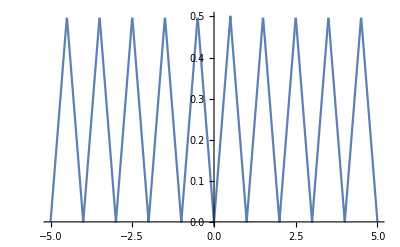
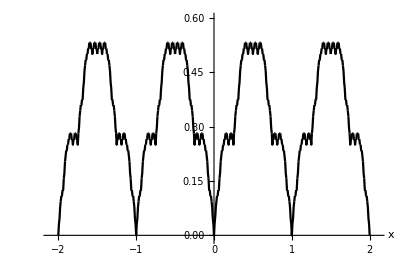
```mathematica
u0[x_]:=Abs[FractionalPart[Abs[x-1/2]]-1/2]
u[x_, k_]:=u0[x*4^k]/4^k
Plot[u[x, 0], {x, -5, 5},AxesStyle->Directive[Black]]
-Graphics-
maxK=3
f[x_]:=Sum[u[x, k], {k, 0, maxK}]
p=Plot[f[x], {x, -2, 2},
MaxRecursion-> 15,
AspectRatio->1/1.5,
LabelStyle->(FontFamily->"STIX Two Text"),
PlotStyle->{Black},
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
PlotRange-> {{-2.1, 2.1}, {-0.01, 0.6}},
AxesLabel->{x,}]
3
-Graphics-
Export["D:\\wolfram\\u_sum.pdf",p]
"D:\\wolfram\\u_sum.pdf"
```